# HW 3 CSCI 561- SUMMER 2017 DATASET - 2

# Data Pre-Processing

In this step data was extracted from the source “https://datarepository.wolframcloud.com/resources/United%2BStates%2Btornadoes%2B1950-2015”.
It consists of the information about the Tornadoes that occurred in U.S. during the period of 1950-2015. The data consists of 12 columns which gives the information about the place, time, loss occurred in property and also the number of humans who were affected due to these tornadoes.

```mathematica
TornadoData=Dataset[ResourceData["Tornadoes in the U.S., 1950-2015"]]
```

Dataset[<>]

The following picture shows the number of tornadoes occurred in each state of U.S. during the period of 1950-2015.

```mathematica
Plots = GeoRegionValuePlot[Rule@@@Tally[ResourceData["Tornadoes in the U.S., 1950-2015"][All,"Location"]],GeoRange->EntityClass["AdministrativeDivision","ContinentalUSStates"]]
```

-Graphics-

We noticed the format of data to be different from a particular row. In view of this point we decided to divide the data at that particular row and process both the parts individually according to the format of data present in it. Dividing the table into two parts. 
Part1 has the EstimatedPropertyLoss column in the form of an interval.
Part2 has the EstimatedPropertyLoss column in a singular numeric form.

```mathematica
part1 = TornadoData[1;;36003]
```

Dataset[<>]

```mathematica
part2 = TornadoData[36004;;61217]
```

Dataset[<>]

After dividing the whole data set into two parts we are now processing the first part. Here in this step we are trying to fill in the missing values in column by replacing them with Interval[{0,0}]. The major idea in doing this operation is to use interpolation in a later step to fill in the values with missing data cells.

```mathematica
ClearingMissingPart1[x_] := If[x === Missing["NotAvailable"],Quantity[Interval[{0,0}],"USDollars"],x]
```

```mathematica
part1 = part1[All,{8->ClearingMissingPart1}]
```

Dataset[<>]

After filling the missing cell values we are trying to convert them into a singular numeric format. We defined a function to convert the value in intervals to singular numeric value by calculating the <mean of start and end of the interval>

```mathematica
MakingSingleValue[Quantity[Interval[{x_,y_}],_]]:= Quantity[(y+x)/2,"USDollars"]
```

```mathematica
part1 = part1[All,{8->MakingSingleValue}]
```

Dataset[<>]

The next step in pre-processing is to process the second part of the data. Here we did the similar step as done on first part to fill the missing cells with value 0.

```mathematica
ClearingMissingPart2[x_] := If[x === Missing["NotAvailable"],Quantity[0,"USDollars"],x]
```

```mathematica
part2 = part2[All,{8->ClearingMissingPart2}]
```

Dataset[<>]

Joining both the parts to get the entire table.

```mathematica
TornadoData = Join[part1,part2]
```

Dataset[<>]

After joining the two parts, we are trying to fill in the missing cells in the column EstimatedCropLoss with a value like we did in the above steps.

```mathematica
ClearMissingInCol[x_] := If[x === Missing["NotAvailable"],Quantity[0,"USDollars"],x]
```

```mathematica
TornadoData = TornadoData[All,{9->ClearMissingInCol}]
```

Dataset[<>]

On studying about how the F-scale is calculated it was noticed the F-scale is calculated based on the total amount of property loss. So considering that point we decided to take the sum of both EstimatedPropertyLoss and EstimatedCropLoss and create a new column TotalLoss.

```mathematica
TornadoData = Append[#,"TotalLoss"-> #["EstimatedPropertyLoss"]+#["EstimatedCropLoss"]]&/@TornadoData
```

Dataset[<>]

```mathematica
PropLoss = Normal[TornadoData[All,"TotalLoss"]]
```

{2750000 $,2750000 $,275000 $,275000 $,27500 $,2750 $,275000 $,275000 $,0 $,27500 $,27500 $,275000 $,275000 $,27500 $,27500 $,27500 $,275000 $,27500 $,0 $,275000 $,2750 $,275000 $,275000 $,275000 $,0 $,27500 $,27500 $,2750 $,27500 $,27500 $,0 $,2750 $,27500 $,27500 $,27500 $,27500 $,275000 $,275000 $,275000 $,0 $,2750 $,0 $,27500 $,0 $,0 $,275000 $,0 $,275000 $,27500 $,0 $,27500 $,2750 $,2750 $,2750 $,27500 $,2750 $,2750 $,27500 $,2750 $,27500 $,27500 $,275000 $,27500 $,275000 $,275000 $,27500 $,275000 $,27500 $,275000 $,27500 $,27500 $,275000 $,275000 $,27500 $,27500 $,275000 $,275000 $,27500 $,275000 $,25 $,27500 $,2750 $,275000 $,275000 $,275000 $,0 $,27500 $,2750 $,2750 $,2750 $,275000 $,27500 $,0 $,27500 $,27500 $,0 $,27500 $,27500 $,27500 $,25 $,275 $,27500 $,0 $,0 $,27500 $,2750 $,2750 $,0 $,27500 $,27500 $,27500 $,2750 $,2750 $,27500 $,275000 $,2750 $,2750 $,0 $,27500 $,2750 $,27500 $,27500 $,2750 $,275 $,0 $,27500 $,27500 $,2750 $,2750 $,0 $,2750 $,27500 $,275000 $,2750000 $,25 $,2750 $,275000 $,2750 $,2750 $,27500 $,275000 $,27500 $,25 $,27500 $,2750 $,2750 $,0 $,27500 $,0 $,0 $,2750 $,27500 $,275000 $,27500 $,275000 $,2750 $,275000 $,27500 $,27500 $,0 $,2750000 $,0 $,27500 $,2750 $,27500 $,275 $,2750 $,275000 $,2750000 $,27500 $,0 $,27500 $,0 $,2750000 $,275 $,0 $,0 $,2750 $,0 $,2750 $,27500 $,27500 $,27500 $,2750 $,275000 $,275 $,0 $,2750 $,27500 $,0 $,2750 $,27500 $,2750 $,275000 $,275 $,2750 $,27500 $,275000 $,275000 $,275000 $,275000 $,27500 $,27500 $,2750000 $,25 $,27500 $,275000 $,2750000 $,2750 $,27500 $,27500 $,27500 $,275 $,0 $,27500 $,2750 $,2750 $,27500 $,27500 $,27500 $,275 $,27500 $,2750 $,275000 $,2750 $,27500 $,275000 $,2750 $,27500 $,0 $,27500 $,27500 $,27500 $,27500 $,0 $,2750 $,2750 $,2750 $,2750 $,0 $,275 $,2750 $,2750 $,2750000 $,27500 $,275000 $,2750 $,2750 $,275000 $,27500 $,2750 $,275 $,275 $,275000 $,275 $,275 $,27500 $,2750 $,27500 $,0 $,27500 $,27500 $,2750 $,2750 $,0 $,2750 $,0 $,0 $,2750 $,275 $,0 $,25 $,2750000 $,2750 $,2750 $,2750 $,2750 $,2750 $,0 $,25 $,275 $,275 $,275000 $,27500 $,275 $,275 $,2750 $,27500 $,27500 $,2750 $,2750 $,275000 $,2750 $,2750 $,275000 $,27500 $,0 $,0 $,27500 $,2750 $,2750 $,2750 $,2750 $,2750 $,2750 $,2750 $,27500 $,2750 $,2750 $,2750 $,0 $,275000 $,2750 $,27500 $,2750 $,27500 $,27500 $,25 $,27500 $,0 $,0 $,0 $,27500 $,60572,0 $,350 000.00 $,500 000.00 $,10 000.00 $,17 000.00 $,0 $,0 $,182 000.00 $,0 $,0 $,0 $,0 $,50 000.00 $,0 $,0 $,0 $,0 $,0 $,0 $,100 000.00 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,50 000.00 $,235 000.00 $,1000000 $,0 $,0 $,2 000.00 $,0 $,0 $,0 $,0 $,500 000.00 $,0 $,0 $,80 000.00 $,0 $,18000000 $,0 $,0 $,5 000.00 $,0 $,0 $,0 $,1 000.00 $,25 000.00 $,0 $,0 $,0 $,15 000.00 $,0 $,50 000.00 $,200 000.00 $,0 $,0 $,0 $,38 000.00 $,0 $,50 000.00 $,100 000.00 $,46 000.00 $,10 000.00 $,40 000.00 $,0 $,0 $,40 000.00 $,20 000.00 $,0 $,0 $,0 $,70 000.00 $,0 $,0 $,0 $,0 $,0 $,1.54e6 $,0 $,0 $,0 $,0 $,4000000 $,12 000.00 $,0 $,0 $,0 $,0 $,1 000.00 $,0 $,0 $,0 $,0 $,10 000.00 $,5 000.00 $,20 000.00 $,0 $,0 $,250 000.00 $,1.5e6 $,50 000.00 $,50 000.00 $,0 $,0 $,50 000.00 $,50 000.00 $,50 000.00 $,200 000.00 $,200 000.00 $,50 000.00 $,75 000.00 $,3000000 $,20 000.00 $,12000000 $,7 000.00 $,200 000.00 $,50 000.00 $,0 $,75 000.00 $,5 000.00 $,0 $,24 000.00 $,0 $,10 000.00 $,7 000.00 $,75 000.00 $,0 $,50 000.00 $,25 000.00 $,25 000.00 $,2 000.00 $,120 000.00 $,10 000.00 $,15 000.00 $,40 000.00 $,25 000.00 $,0 $,1.45e6 $,405 000.00 $,125 000.00 $,0 $,1 000.00 $,5 000.00 $,3 000.00 $,25 000.00 $,5 000.00 $,5 000.00 $,0 $,10 000.00 $,350 000.00 $,25 000.00 $,350 000.00 $,1 000.00 $,1 000.00 $,76 000.00 $,0 $,0 $,0 $,0 $,1.2e6 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,83 000.00 $,0 $,0 $,0 $,50 000.00 $,50 000.00 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,0 $,7 000.00 $,0 $,0 $,210 000.00 $,500 000.00 $,200 000.00 $,150 000.00 $,10 000.00 $,83 000.00 $,12 000.00 $,10 000.00 $,50 000.00 $,5 000.00 $,40 000.00 $,13 000.00 $,13 000.00 $,8 000.00 $,20 000.00 $,100 000.00 $,8 000.00 $,0 $,0 $,50 000.00 $,150 000.00 $,60 000.00 $,0 $,311 000.00 $,0 $,0 $,2000000 $,35 000.00 $,10 000.00 $,0 $,0 $,2000000 $,10 000.00 $,10 000.00 $,18 000.00 $,80 000.00 $,90 000.00 $,5 000.00 $,50 000.00 $,5 000.00 $,175 000.00 $,13 000.00 $,75 000.00 $,25 000.00 $,2.354e6 $,50 000.00 $,100 000.00 $,25 000.00 $,3 000.00 $,150 000.00 $,9.465e6 $,1.0922e7 $,6 000.00 $,0 $,0 $,0 $,25 000.00 $,1.457e6 $,0 $,500 000.00 $,100 000.00 $,2000000 $,5.21e6 $,0 $,100 000.00 $,100 000.00 $,120 000.00 $,400 000.00 $,100 000.00 $,0 $,0 $,15 000.00 $,1000000 $,20 000.00 $,50 000.00 $,0 $,12 000.00 $,0 $,0 $,15 000.00 $,10 000.00 $,0 $,20 000.00 $,0 $,0 $,9.729e6 $,2.68e7 $,40 000.00 $,1.4e6 $,1.5e6 $,600 000.00 $,15 000.00 $,45 000.00 $,150 000.00 $,15 000.00 $,55 000.00 $,100 000.00 $,300 000.00 $,75 000.00 $,0 $,60 000.00 $,5 000.00 $,250 000.00 $,0 $,0 $,0 $,50 000.00 $,100 000.00 $,10 000.00 $,50 000.00 $}
 |  |  |  |

As mentioned in one of the previous steps regarding interpolation. We are in an assumption that whenever a tornado occurs the property loss definitely occurs which can be either crop loss or property loss. By performing the next step we make sure that no cell in the column TotalLoss has $0 in the cell. 

We used interpolation as it can give a value that can be very similar to the real-life data as the function is formed from the real-life data.

```mathematica
f = Interpolation[PropLoss]
```

InterpolatingFunction[{{1., 61217.}}, <>]

The following diagram shoes the plot of the function interpolated from the existing values in the range of {1,1000}.

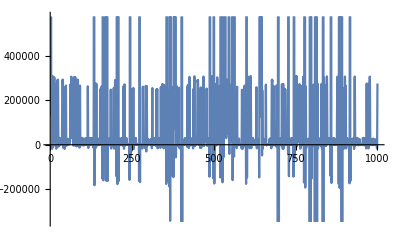

```mathematica
Plot[f[x],{x,1,1000}]
```

To calculate the value at missing cells we tried to generate a random value which is a real number by nature so that it derives a value very near to the real-life. Using this interpolation we obtained few values to be negative. As the property loss cannot be in negative we converted them into positive values in the next step.

```mathematica
calPropLoss[x_] := If[x==Quantity[0,"USDollars"], f[RandomReal[{1,61217}]],x]
```

```mathematica
TornadoData = TornadoData[All,{13->calPropLoss}]
```

Dataset[<>]

```mathematica
makePositive[x_] := If[x<Quantity[0,"USDollars"],x*(-1),x]
```

```mathematica
TornadoData = TornadoData[All,{13->makePositive}]
```

Dataset[<>]

Now considering the columns Start and End, we noticed that there are many cells with missing values. To get our training data in a functional manner we need to fill in these values with co-ordinates such that they look close to the real time data. To bring this idea alive we filled all the missing values with the co-ordinates of Texas state as it is one of the states that is present in the center of U.S.

```mathematica
FillingCords = GeoPosition[TornadoData[18,1]]
```

GeoPosition[{32.7403,-89.6678}]

```mathematica
Cords[x_]:=If[x===Missing["NotAvailable"],FillingCords,x]
```

```mathematica
TornadoData = TornadoData[All,{10->Cords}]
```

Dataset[<>]

```mathematica
TornadoData = TornadoData[All,{11->Cords}]
```

Dataset[<>]

After reading the document on how the F-scale is calculated it was noticed that the scale calculation depends on the distance covered by the tornado. Utilizing the co-ordinates present in Start and End column we found the distance the tornado covered in miles and placed them in a new column called Distance. 

In the next step we performed a mathematical operation on the all the data in “Distance” which has its value more than 200 miles because of filling the co-ordinates of Texas in missing cells. The reason for using the value 25 is on examining the data it was noticed that no tornado covered more than that distance.

```mathematica
TornadoData = Append[#,"Distance"-> GeoDistance[#["Start"],#["End"]]]&/@TornadoData
```

Dataset[<>]

We made an additional column HumanDamage which is the sum of column Injuries and Fatalities. The reason to form this column is to test the algorithm with different features to obtain good accuracy.
In the next step we tried to obtain only the quantity magnitude(RemoveUnits[]) ,so that the features go well in the implementation of the Decision Tree chosen.

```mathematica
RemoveUnits[x_] := QuantityMagnitude[x]
```

```mathematica
TornadoData = TornadoData[All,{7->RemoveUnits}]
```

Dataset[<>]

```mathematica
TornadoData = TornadoData[All,{13->RemoveUnits}]
```

Dataset[<>]

```mathematica
TornadoData = TornadoData[All,{14->RemoveUnits}]
```

Dataset[<>]

```mathematica
TornadoData = Append[#,"HumanDamage"-> #["Injuries"]+#["Fatalities"]]&/@TornadoData
```

Dataset[<>]

```mathematica
DistanceChange[x_] := If[x>100,Mod[x,25],x]
```

```mathematica
TornadoData = TornadoData[All,{14->DistanceChange}]
```

Dataset[<>]

The purpose of performing this step is to utilize the update in the scaling of the tornado. After year <> the scaling of tornado has changed to EF-scale. So we decided to extract the Year in which the tornado occurred which can help the decision tree very well with the format and also simplicity in the data. The new column is named as “YearOccured”.

```mathematica
calcYear[x_]:=DateValue[x,"Year"]
TornadoData=Append[#,"YearOccured"->calcYear[#["Date"]]]&/@TornadoData
```

Dataset[<>]

# Feature Selection

The following columns TotalLoss, Distance, HumanDamage and Date as features to predict the magnitude of the Tornado.

```mathematica
Features = Map[{#TotalLoss,#Distance,#HumanDamage,#Date}->#Magnitude&,Normal[TornadoData]]
```

{{2750000,11.0595,3,Sat 31 Dec 1949 03:11:00CDT}→F3,{2750000,6.40594,3,Sat 31 Dec 1949 03:11:00CDT}→F3,{275000,4.9051,0,Sat 31 Dec 1949 03:11:10CDT}→F3,{275000,4.00706,3,Sat 31 Dec 1949 03:11:55CDT}→F3,{27500,2.88964,1,Sat 31 Dec 1949 03:16:00CDT}→F1,61208,{50000.,5.7353,0,Mon 30 Nov 2015 04:04:46CDT}→EF2,{100000.,5.58162,0,Mon 30 Nov 2015 04:05:43CDT}→EF1,{10000.,0.774609,0,Mon 30 Nov 2015 04:08:30CDT}→EF1,{50000.,0.924498,0,Mon 30 Nov 2015 04:15:58CDT}→EF0}
 |  |  |  |

Extracting the training data and testing data.

```mathematica
training = Drop[Features,{1,-1,5}]
testing = Take[Features,{1,-1,5}]
```

{{2750000,6.40594,3,Sat 31 Dec 1949 03:11:00CDT}→F3,{275000,4.9051,0,Sat 31 Dec 1949 03:11:10CDT}→F3,{275000,4.00706,3,Sat 31 Dec 1949 03:11:55CDT}→F3,{27500,2.88964,1,Sat 31 Dec 1949 03:16:00CDT}→F1,{275000,2.64374,5,Sat 31 Dec 1949 01:19:30CDT}→F2,48964,{1957.81,0.603913,0,Mon 30 Nov 2015 04:03:20CDT}→EF1,{50000.,5.7353,0,Mon 30 Nov 2015 04:04:46CDT}→EF2,{100000.,5.58162,0,Mon 30 Nov 2015 04:05:43CDT}→EF1,{50000.,0.924498,0,Mon 30 Nov 2015 04:15:58CDT}→EF0}
 |  |  |  |

{{2750000,11.0595,3,Sat 31 Dec 1949 03:11:00CDT}→F3,{2750,19.3726,2,Sat 31 Dec 1949 13:05:25CDT}→F3,{27500,11.4229,13,Tue 31 Jan 1950 11:13:50CDT}→F3,{27500,3.44485,0,Tue 31 Jan 1950 12:06:10CDT}→F2,12236,{150000.,7.08765,0,Mon 30 Nov 2015 03:15:32CDT}→EF1,{75000.,7.09325,0,Mon 30 Nov 2015 03:17:06CDT}→EF1,{291056.,24.3545,0,Mon 30 Nov 2015 03:23:10CDT}→EF1,{10000.,0.774609,0,Mon 30 Nov 2015 04:08:30CDT}→EF1}
 |  |  |  |

# Machine Learning algorithm application

## Neural Networks

ClassifierFunction[…]

0.55129

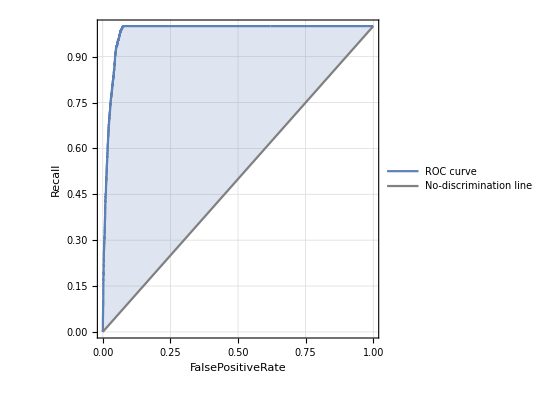
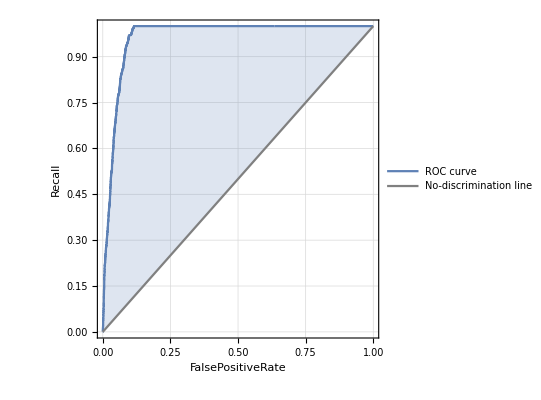
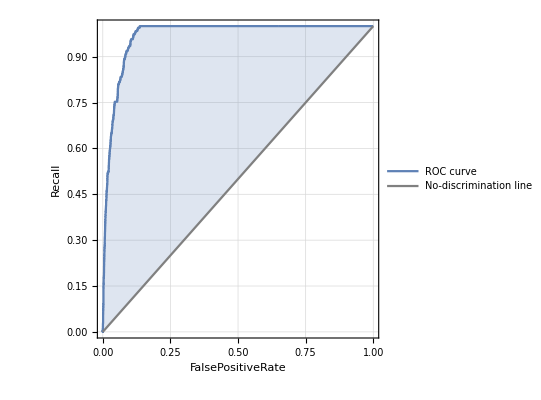
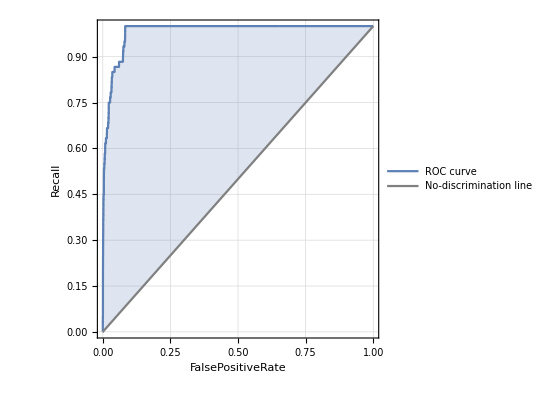
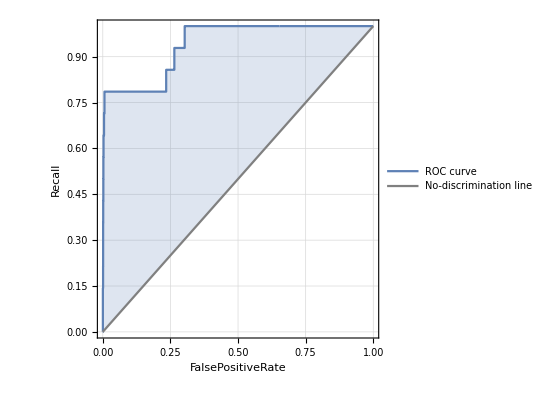
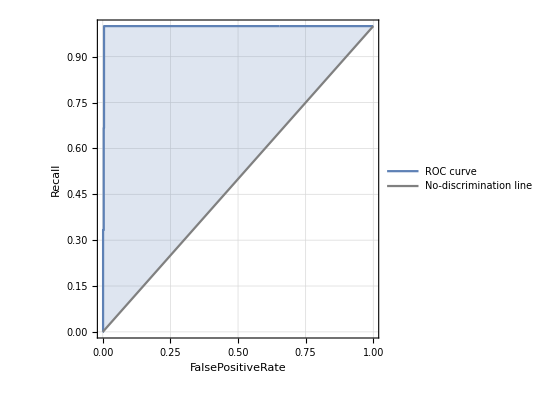
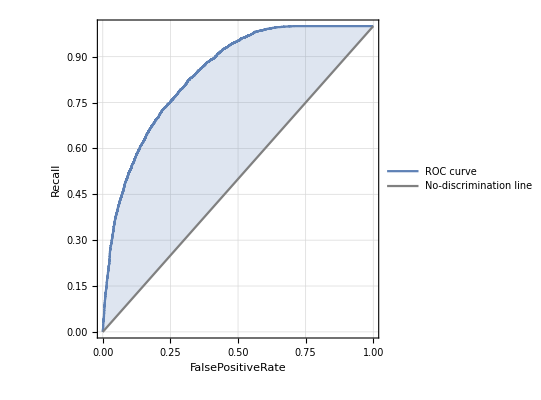
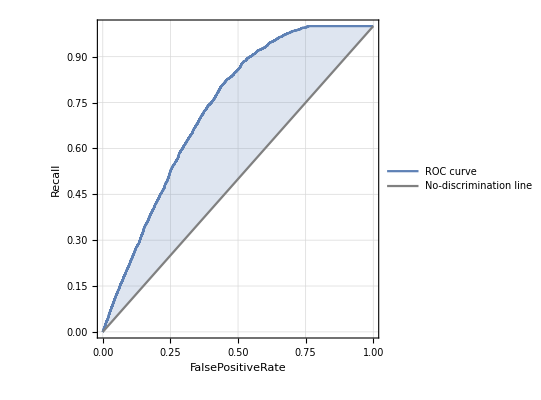
<|EF0→-Graphics-,EF1→-Graphics-,EF2→-Graphics-,EF3→-Graphics-,EF4→-Graphics-,EF5→-Graphics-,F0→-Graphics-,F1→-Graphics-,F2→-Graphics-,F3→-Graphics-,F4→-Graphics-,F5→-Graphics-|>

<|EF0→0.708048,EF1→0.470985,EF2→0.457143,EF3→0.45,EF4→Indeterminate,EF5→0.,F0→0.646756,F1→0.454079,F2→0.375,F3→0.429204,F4→0.531646,F5→Indeterminate|>

```mathematica
NNclassifier=Classify[training,Method->"NeuralNetwork"]
ClassifierMeasurements[NNclassifier,testing,"Accuracy"]
ClassifierMeasurements[NNclassifier,testing,"ROCCurve"]
ClassifierMeasurements[NNclassifier,testing,"Precision"]
ClassifierMeasurements[NNclassifier,testing,"Recall"]
```

## Decision Trees

```mathematica
examples=Map[{#TotalLoss,#Distance,#YearOccured,#HumanDamage,#Magnitude}&,Normal[TornadoData]]

trainingdt=Drop[examples,{1,-1,5}];
testingdt=Take[examples,{1,-1,5}];


Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/AVCDecisionTreeForest.m"]

dtree=BuildDecisionTree[trainingdt,{5,0},"ImpurityFunction"->"Gini"]


classResRules=DecisionTreeClassificationSuccess[dtree,testingdt]
```

{{2750000,11.0595,1949,3,F3},{2750000,6.40594,1949,3,F3},{275000,4.9051,1949,0,F3},{275000,4.00706,1949,3,F3},{27500,2.88964,1949,1,F1},{2750,19.3726,1949,2,F3},{275000,2.64374,1949,5,F2},61203,{74045.,24.3545,2015,0,EF1},{137288.,1.94351,2015,0,EF1},{138303.,0.603913,2015,0,EF1},{50000.,5.7353,2015,0,EF2},{100000.,5.58162,2015,0,EF1},{10000.,0.774609,2015,0,EF1},{50000.,0.924498,2015,0,EF0}}
 |  |  |  |

{{0.102447,50177/25,3,Number,48973},{1},{1}}
 |  |  |  |

This image represents the graph plot of the decision tree formed. The reason for attaching the image is, it is taking high amount of time to  create the graph on evaluating the notebook. This image can be used to infer regarding the decision tree formed.

{{EF0,True}→0.700909,{EF0,False}→0.299091,{EF1,True}→0.429907,{EF1,False}→0.570093,{EF2,True}→0.258065,{EF2,False}→0.741935,{EF3,True}→0.2,{EF3,False}→0.8,{EF4,True}→0.357143,{EF4,False}→0.642857,{EF5,True}→0.,{EF5,False}→1.,{F0,True}→0.72397,{F0,False}→0.27603,{F1,True}→0.475466,{F1,False}→0.524534,{F2,True}→0.313163,{F2,False}→0.686837,{F3,True}→0.215164,{F3,False}→0.784836,{F4,True}→0.180451,{F4,False}→0.819549,{F5,True}→0.1875,{F5,False}→0.8125,{All,True}→0.544838,{All,False}→0.455162}

Accuracy Achieved = 0.544838
Precision, Recall and ROC curve can be interpreted from the following values:
{“EF0”,True}→0.700909,{“EF0”,False}→0.299091,{“EF1”,True}→0.429907,{“EF1”,False}→0.570093,{“EF2”,True}→0.258065,{“EF2”,False}→0.741935,{“EF3”,True}→0.2,{“EF3”,False}→0.8,{“EF4”,True}→0.357143,{“EF4”,False}→0.642857,{“EF5”,True}→0.,{“EF5”,False}→1.,{“F0”,True}→0.72397,{“F0”,False}→0.27603,{“F1”,True}→0.475466,{“F1”,False}→0.524534,{“F2”,True}→0.313163,{“F2”,False}→0.686837,{“F3”,True}→0.215164,{“F3”,False}→0.784836,{“F4”,True}→0.180451,{“F4”,False}→0.819549,{“F5”,True}→0.1875,{“F5”,False}→0.8125,{All,True}→0.544838,{All,False}→0.455162}

## Naive Bayes

```mathematica
NBclassifier=Classify[training,Method->"NaiveBayes"]
```

ClassifierFunction[…]

```mathematica
AccuracyMeasure = ClassifierMeasurements[NBclassifier,testing,"Accuracy"]
```

0.559213

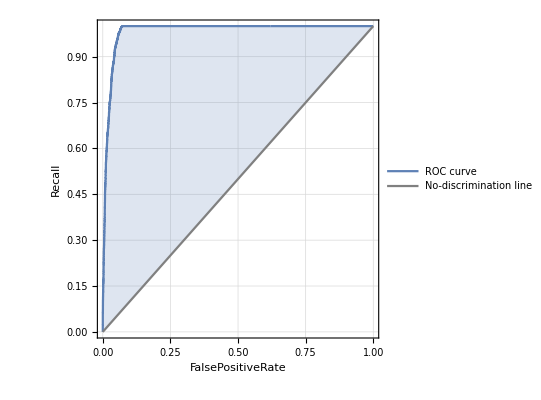
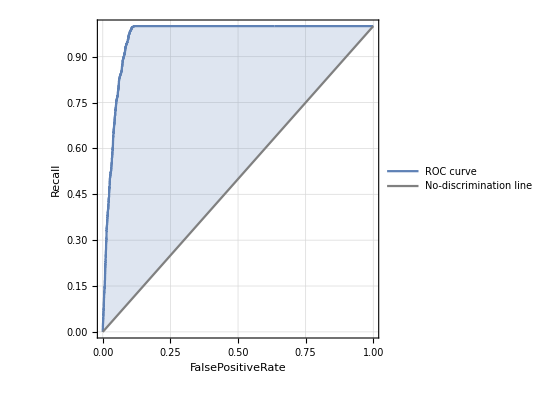
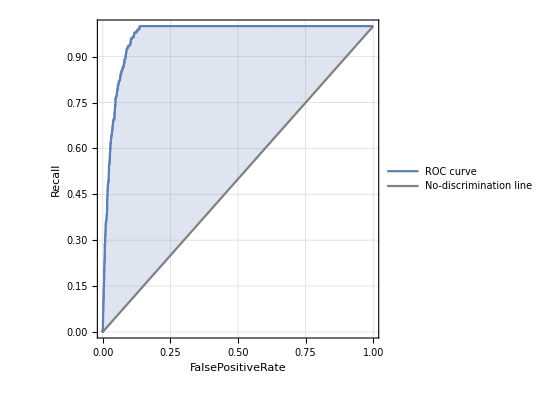
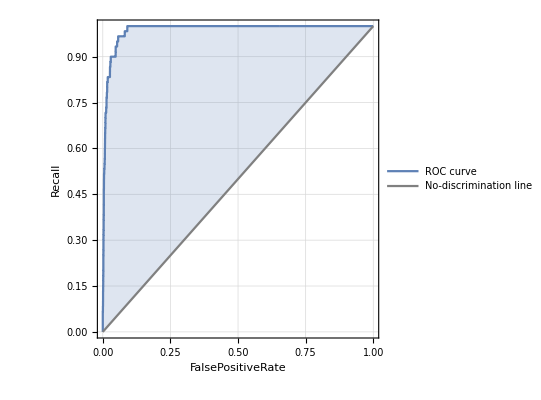
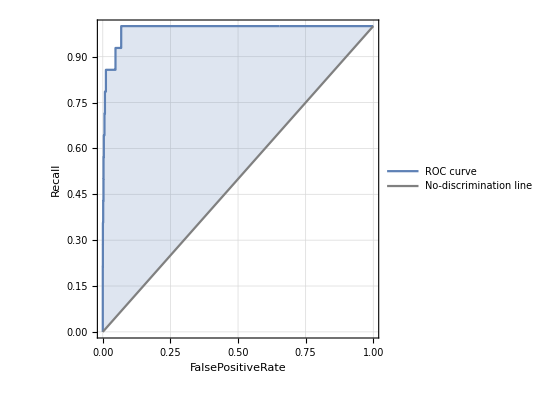
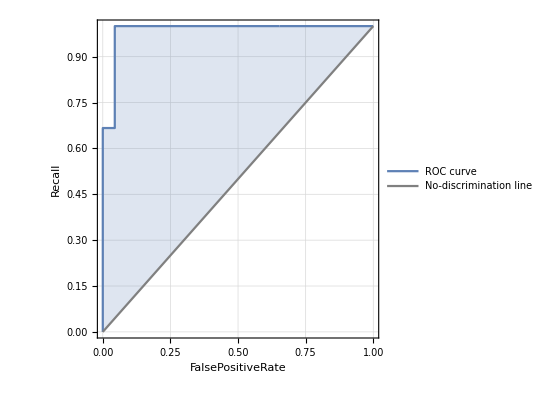
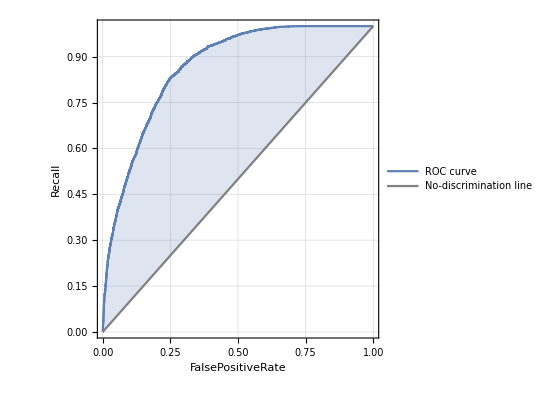
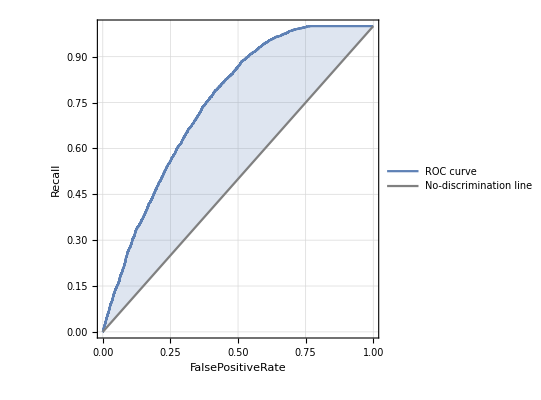
<|EF0→-Graphics-,EF1→-Graphics-,EF2→-Graphics-,EF3→-Graphics-,EF4→-Graphics-,EF5→-Graphics-,F0→-Graphics-,F1→-Graphics-,F2→-Graphics-,F3→-Graphics-,F4→-Graphics-,F5→-Graphics-|>

```mathematica
ClassifierMeasurements[NBclassifier,testing,"ROCCurve"]
```

```mathematica
ClassifierMeasurements[NBclassifier,testing,"Precision"]
```

<|EF0→0.721943,EF1→0.509402,EF2→0.343558,EF3→0.346939,EF4→0.294118,EF5→0.4,F0→0.700467,F1→0.480979,F2→0.365227,F3→0.376093,F4→0.314516,F5→0.0638298|>

```mathematica
ClassifierMeasurements[NBclassifier,testing,"Recall"]
```

<|EF0→0.783636,EF1→0.464174,EF2→0.301075,EF3→0.283333,EF4→0.357143,EF5→0.666667,F0→0.697829,F1→0.468006,F2→0.416719,F3→0.264344,F4→0.293233,F5→0.1875|>

# Comparisons

After applying the above algorithms we can see that the overall results achieved by the all the algorithms are very near. But when we compared them class wise we can see that the classes with label EF0 and F0 have higher success rates compared to the classes EF5 and F5. This occurs due to the amount of the data present with respect to each class in the given dataset. From these evaluation we can say that Dataset had more tornadoes of class EF0 and F0 compared to EF5 and F5 and the algorithms learned more about EF0 and F0 compared to EF5 and F5. The values of success had decreased consistently from EF0-EF5 and F0-F5 because in real life also large number of tornadoes occurred are of class EF0(F0) then EF1(F1) and so on till EF5(F5). Tornadoes with high severity of F5 and EF5 did not occur in considerable number.

From the above evaluation we can definitely infer that for an algorithm to learn very well there should be uniform distribution of all classes in the training data. Different proportions can sometimes cause over-fitting and under-fitting of the data.

# References:

1.	Wolfram Research, “Tornadoes in the U.S., 1950-2015” from the Wolfram Data Repository. (2016) https://doi.org/10.24097/wolfram.33875.data
2.	Decision Tree adopted from the following link: https://github.com/antononcube/MathematicaForPrediction/blob/master/AVCDecisionTreeForest.m